## Wigner 𝒟 Matrix

Following Goldberg et al. (1967), Eq. (3.9):

```mathematica
𝒟[l_,mp_,m_,α_,β_,γ_]:=√(((l+m)!(l-m)!)/((l+mp)!(l-mp)!))Simplify[∑_(ρ=Max[0,m+mp])^Min[l+mp,l+m] (Binomial[l+mp,ρ]Binomial[l-mp,ρ-m-mp](-1)^(l+mp-ρ)ⅇ^(ⅈ m α)Cos[β1/2]^(2ρ-m-mp)Sin[β1/2]^(2l-2ρ+m+mp) ⅇ^(ⅈ mp γ))/.{α1->α,β1->β,γ1->γ}];
```

### Tests

Testing a few relations that should be true.  A 0 indicates that the test is passed.

#### 𝒟[l, mp, m, α, β, γ]* == 𝒟[l, mp, m, -α, β, -γ]

```mathematica
Table[FullSimplify[𝒟[l,mp,m,α,β,γ]*-𝒟[l,mp,m,-α,β,-γ],Assumptions->{l∈Integers,m∈Integers,mp∈Integers,l≥m,l≥mp,α∈Reals,β∈Reals,γ∈Reals}],{l,0,5},{m,-l,l},{mp,-l,l}]
```

{{{0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}}}

#### 𝒟[l, m, mp, α, β, γ] == 𝒟[l, mp, m, γ, -β, α]

```mathematica
Table[FullSimplify[𝒟[l,m,mp,α,β,γ]-𝒟[l,mp,m,γ,-β,α],Assumptions->{l∈Integers,m∈Integers,mp∈Integers,l≥m,l≥mp,α∈Reals,β∈Reals,γ∈Reals}],{l,0,5},{m,-l,l},{mp,-l,l}]
```

{{{0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}}}

#### 𝒟[l, -mp, m, α, β, γ] == (-1)^(l-mp)𝒟[l, mp, m, α, β+π, -γ]

```mathematica
Table[FullSimplify[𝒟[l,-mp,m,α,β,γ]-(-1)^(l-mp)𝒟[l,mp,m,α,β+π,-γ],Assumptions->{l∈Integers,m∈Integers,mp∈Integers,l≥m,l≥mp,α∈Reals,β∈Reals,γ∈Reals}],{l,0,5},{m,-l,l},{mp,-l,l}]
```

{{{0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0}}}

#### Misc.

```mathematica
l=1;
m=1;
Table[SphericalHarmonicY[l,mp,θ,ϕ+α],{mp,-l,l}]
Table[𝒟[l,mp,m,α,β,0],{mp,-l,l}]
FullSimplify[∑_(mp=-l)^l SphericalHarmonicY[l,mp,θ,ϕ]𝒟[l,mp,m,α,β,0]]
l=.;
m=.;
```

{1/2 ⅇ^(-ⅈ α-ⅈ ϕ) √(3/(2 π)) Sin[θ],1/2 √(3/π) Cos[θ],-1/2 ⅇ^(ⅈ α+ⅈ ϕ) √(3/(2 π)) Sin[θ]}

{ⅇ^(ⅈ α) Sin[β/2]^2,(ⅇ^(ⅈ α) Sin[β])/(√2),ⅇ^(ⅈ α) Cos[β/2]^2}

1/2 ⅇ^(ⅈ α) √(3/(2 π)) (Cos[θ] Sin[β]-Sin[θ] (Cos[β] Cos[ϕ]+ⅈ Sin[ϕ]))

## Spin-Weighted Spherical Harmonics

Following Goldberg et al. (1967), Eq. (3.11), with the inclusion of the Condon-Shortley phase:

```mathematica
Y[s_,l_,m_,θ_,ϕ_]:=Simplify[(-1)^m √((2l+1)/(4π))𝒟[l,-s,m,ϕ,θ1,0]/.θ1->θ];
```

### Values

```mathematica
s=-2;
Table[{s,l,m,FullSimplify[Y[s,l,m,θ,ϕ],Assumptions->{ϕ∈Reals,θ∈Reals}]},{l,Abs[s],Abs[s]+6},{m,l,-l,-1}]//MatrixForm
s=.;
```

({{-2,2,2,1/2 ⅇ^(2 ⅈ ϕ) √(5/π) Cos[θ/2]^4},{-2,2,1,1/4 ⅇ^(ⅈ ϕ) √(5/π) (1+Cos[θ]) Sin[θ]},{-2,2,0,1/4 √(15/(2 π)) Sin[θ]^2},{-2,2,-1,1/2 ⅇ^(-ⅈ ϕ) √(5/π) Sin[θ/2]^2 Sin[θ]},{-2,2,-2,1/2 ⅇ^(-2 ⅈ ϕ) √(5/π) Sin[θ/2]^4}}
{{-2,3,3,-ⅇ^(3 ⅈ ϕ) √(21/(2 π)) Cos[θ/2]^5 Sin[θ/2]},{-2,3,2,1/2 ⅇ^(2 ⅈ ϕ) √(7/π) Cos[θ/2]^4 (-2+3 Cos[θ])},{-2,3,1,-1/32 ⅇ^(ⅈ ϕ) √(35/(2 π)) (Sin[θ]-4 Sin[2 θ]-3 Sin[3 θ])},{-2,3,0,1/4 √(105/(2 π)) Cos[θ] Sin[θ]^2},{-2,3,-1,1/32 ⅇ^(-ⅈ ϕ) √(35/(2 π)) (Sin[θ]+4 Sin[2 θ]-3 Sin[3 θ])},{-2,3,-2,1/2 ⅇ^(-2 ⅈ ϕ) √(7/π) (2+3 Cos[θ]) Sin[θ/2]^4},{-2,3,-3,1/2 ⅇ^(-3 ⅈ ϕ) √(21/(2 π)) Sin[θ/2]^4 Sin[θ]}}
{{-2,4,4,3/64 ⅇ^(4 ⅈ ϕ) √(7/π) Csc[θ/2]^4 Sin[θ]^6},{-2,4,3,-3 ⅇ^(3 ⅈ ϕ) √(7/(2 π)) Cos[θ/2]^5 (-1+2 Cos[θ]) Sin[θ/2]},{-2,4,2,(3 ⅇ^(2 ⅈ ϕ) Cos[θ/2]^4 (9-14 Cos[θ]+7 Cos[2 θ]))/(4 √π)},{-2,4,1,(3 ⅇ^(ⅈ ϕ) (3 Sin[θ]-2 Sin[2 θ]+7 (Sin[3 θ]+Sin[4 θ])))/(32 √(2 π))},{-2,4,0,3/16 √(5/(2 π)) (5+7 Cos[2 θ]) Sin[θ]^2},{-2,4,-1,(3 ⅇ^(-ⅈ ϕ) (3 Sin[θ]+2 Sin[2 θ]+7 Sin[3 θ]-7 Sin[4 θ]))/(32 √(2 π))},{-2,4,-2,(3 ⅇ^(-2 ⅈ ϕ) (9+14 Cos[θ]+7 Cos[2 θ]) Sin[θ/2]^4)/(4 √π)},{-2,4,-3,3 ⅇ^(-3 ⅈ ϕ) √(7/(2 π)) (2 Cos[θ/2]+Cos[(3 θ)/2]) Sin[θ/2]^5},{-2,4,-4,3/4 ⅇ^(-4 ⅈ ϕ) √(7/π) Sin[θ/2]^4 Sin[θ]^2}}
{{-2,5,5,-ⅇ^(5 ⅈ ϕ) √(330/π) Cos[θ/2]^7 Sin[θ/2]^3},{-2,5,4,ⅇ^(4 ⅈ ϕ) √(33/π) Cos[θ/2]^6 (-2+5 Cos[θ]) Sin[θ/2]^2},{-2,5,3,-1/4 ⅇ^(3 ⅈ ϕ) √(33/(2 π)) Cos[θ/2]^5 (17-24 Cos[θ]+15 Cos[2 θ]) Sin[θ/2]},{-2,5,2,1/8 ⅇ^(2 ⅈ ϕ) √(11/π) Cos[θ/2]^4 (-32+57 Cos[θ]-36 Cos[2 θ]+15 Cos[3 θ])},{-2,5,1,1/256 ⅇ^(ⅈ ϕ) √(77/π) (-2 Sin[θ]+8 Sin[2 θ]-3 Sin[3 θ]+12 Sin[4 θ]+15 Sin[5 θ])},{-2,5,0,1/32 √(1155/(2 π)) (5 Cos[θ]+3 Cos[3 θ]) Sin[θ]^2},{-2,5,-1,1/256 ⅇ^(-ⅈ ϕ) √(77/π) (2 Sin[θ]+8 Sin[2 θ]+3 (Sin[3 θ]+4 Sin[4 θ]-5 Sin[5 θ]))},{-2,5,-2,1/8 ⅇ^(-2 ⅈ ϕ) √(11/π) (32+57 Cos[θ]+36 Cos[2 θ]+15 Cos[3 θ]) Sin[θ/2]^4},{-2,5,-3,1/8 ⅇ^(-3 ⅈ ϕ) √(33/(2 π)) (58 Cos[θ/2]+39 Cos[(3 θ)/2]+15 Cos[(5 θ)/2]) Sin[θ/2]^5},{-2,5,-4,ⅇ^(-4 ⅈ ϕ) √(33/π) Cos[θ/2]^2 (2+5 Cos[θ]) Sin[θ/2]^6},{-2,5,-5,ⅇ^(-5 ⅈ ϕ) √(330/π) Cos[θ/2]^3 Sin[θ/2]^7}}
{{-2,6,6,3/512 ⅇ^(6 ⅈ ϕ) √(715/π) Csc[θ/2]^4 Sin[θ]^8},{-2,6,5,-1/2 ⅇ^(5 ⅈ ϕ) √(2145/π) Cos[θ/2]^7 (-1+3 Cos[θ]) Sin[θ/2]^3},{-2,6,4,1/8 ⅇ^(4 ⅈ ϕ) √(195/(2 π)) Cos[θ/2]^6 (35-44 Cos[θ]+33 Cos[2 θ]) Sin[θ/2]^2},{-2,6,3,-3/32 ⅇ^(3 ⅈ ϕ) √(13/π) Cos[θ/2]^5 (-98+185 Cos[θ]-110 Cos[2 θ]+55 Cos[3 θ]) Sin[θ/2]},{-2,6,2,1/256 ⅇ^(2 ⅈ ϕ) √(13/π) Cos[θ/2]^4 (1709-3096 Cos[θ]+2340 Cos[2 θ]-1320 Cos[3 θ]+495 Cos[4 θ])},{-2,6,1,(ⅇ^(ⅈ ϕ) √(65/(2 π)) (20 Sin[θ]-17 Sin[2 θ]+54 Sin[3 θ]-12 Sin[4 θ]+66 Sin[5 θ]+99 Sin[6 θ]))/1024},{-2,6,0,1/512 √(1365/π) (35+60 Cos[2 θ]+33 Cos[4 θ]) Sin[θ]^2},{-2,6,-1,(ⅇ^(-ⅈ ϕ) √(65/(2 π)) (20 Sin[θ]+17 Sin[2 θ]+54 Sin[3 θ]+12 Sin[4 θ]+66 Sin[5 θ]-99 Sin[6 θ]))/1024},{-2,6,-2,1/256 ⅇ^(-2 ⅈ ϕ) √(13/π) (1709+3096 Cos[θ]+2340 Cos[2 θ]+1320 Cos[3 θ]+495 Cos[4 θ]) Sin[θ/2]^4},{-2,6,-3,(3 ⅇ^(-3 ⅈ ϕ) √(13/π) (20 Sin[θ]+51 Sin[2 θ]+6 Sin[3 θ]+20 Sin[4 θ]-110 Sin[5 θ]+55 Sin[6 θ]))/2048},{-2,6,-4,1/8 ⅇ^(-4 ⅈ ϕ) √(195/(2 π)) Cos[θ/2]^2 (35+44 Cos[θ]+33 Cos[2 θ]) Sin[θ/2]^6},{-2,6,-5,1/2 ⅇ^(-5 ⅈ ϕ) √(2145/π) Cos[θ/2]^3 (1+3 Cos[θ]) Sin[θ/2]^7},{-2,6,-6,3/32 ⅇ^(-6 ⅈ ϕ) √(715/π) Sin[θ/2]^4 Sin[θ]^4}}
{{-2,7,7,-ⅇ^(7 ⅈ ϕ) √(15015/(2 π)) Cos[θ/2]^9 Sin[θ/2]^5},{-2,7,6,1/2 ⅇ^(6 ⅈ ϕ) √(2145/π) Cos[θ/2]^8 (-2+7 Cos[θ]) Sin[θ/2]^4},{-2,7,5,-1/8 ⅇ^(5 ⅈ ϕ) √(165/(2 π)) Cos[θ/2]^7 (93-104 Cos[θ]+91 Cos[2 θ]) Sin[θ/2]^3},{-2,7,4,1/16 ⅇ^(4 ⅈ ϕ) √(165/(2 π)) Cos[θ/2]^6 (-140+285 Cos[θ]-156 Cos[2 θ]+91 Cos[3 θ]) Sin[θ/2]^2},{-2,7,3,-1/128 ⅇ^(3 ⅈ ϕ) √(15/(2 π)) Cos[θ/2]^5 (3115-5456 Cos[θ]+4268 Cos[2 θ]-2288 Cos[3 θ]+1001 Cos[4 θ]) Sin[θ/2]},{-2,7,2,(ⅇ^(2 ⅈ ϕ) √(15/π) (675 Cos[θ]+200 Cos[2 θ]+361 Cos[3 θ]+11 (64 Cos[4 θ]+Cos[5 θ]+104 Cos[6 θ]+91 Cos[7 θ])))/8192},{-2,7,1,-(3 ⅇ^(ⅈ ϕ) √(5/(2 π)) (75 Sin[θ]-300 Sin[2 θ]+171 Sin[3 θ]-11 (48 Sin[4 θ]-5 Sin[5 θ]+52 Sin[6 θ]+91 Sin[7 θ])))/8192},{-2,7,0,(3 √(35/π) (350 Cos[θ]+275 Cos[3 θ]+143 Cos[5 θ]) Sin[θ]^2)/1024},{-2,7,-1,(3 ⅇ^(-ⅈ ϕ) √(5/(2 π)) (75 Sin[θ]+300 Sin[2 θ]+171 Sin[3 θ]+11 (48 Sin[4 θ]+5 Sin[5 θ]+52 Sin[6 θ]-91 Sin[7 θ])))/8192},{-2,7,-2,1/512 ⅇ^(-2 ⅈ ϕ) √(15/π) (5220+9810 Cos[θ]+7920 Cos[2 θ]+5445 Cos[3 θ]+2860 Cos[4 θ]+1001 Cos[5 θ]) Sin[θ/2]^4},{-2,7,-3,(ⅇ^(-3 ⅈ ϕ) √(15/(2 π)) (405 Sin[θ]+380 Sin[2 θ]+741 Sin[3 θ]+11 (-16 Sin[4 θ]+11 Sin[5 θ]-156 Sin[6 θ]+91 Sin[7 θ])))/8192},{-2,7,-4,1/16 ⅇ^(-4 ⅈ ϕ) √(165/(2 π)) Cos[θ/2]^2 (140+285 Cos[θ]+156 Cos[2 θ]+91 Cos[3 θ]) Sin[θ/2]^6},{-2,7,-5,1/8 ⅇ^(-5 ⅈ ϕ) √(165/(2 π)) Cos[θ/2]^3 (93+104 Cos[θ]+91 Cos[2 θ]) Sin[θ/2]^7},{-2,7,-6,1/2 ⅇ^(-6 ⅈ ϕ) √(2145/π) Cos[θ/2]^4 (2+7 Cos[θ]) Sin[θ/2]^8},{-2,7,-7,ⅇ^(-7 ⅈ ϕ) √(15015/(2 π)) Cos[θ/2]^5 Sin[θ/2]^9}}
{{-2,8,8,ⅇ^(8 ⅈ ϕ) √(34034/π) Cos[θ/2]^10 Sin[θ/2]^6},{-2,8,7,-ⅇ^(7 ⅈ ϕ) √(17017/(2 π)) Cos[θ/2]^9 (-1+4 Cos[θ]) Sin[θ/2]^5},{-2,8,6,1/2 ⅇ^(6 ⅈ ϕ) √(255255/π) Cos[θ/2]^8 (1-Cos[θ]+Cos[2 θ]) Sin[θ/2]^4},{-2,8,5,-1/8 ⅇ^(5 ⅈ ϕ) √(12155/(2 π)) Cos[θ/2]^7 (-19+42 Cos[θ]-21 Cos[2 θ]+14 Cos[3 θ]) Sin[θ/2]^3},{-2,8,4,1/32 ⅇ^(4 ⅈ ϕ) √(935/(2 π)) Cos[θ/2]^6 (265-442 Cos[θ]+364 Cos[2 θ]-182 Cos[3 θ]+91 Cos[4 θ]) Sin[θ/2]^2},{-2,8,3,(ⅇ^(3 ⅈ ϕ) √(561/(2 π)) (35 Sin[θ]-96 Sin[2 θ]+51 Sin[3 θ]-100 Sin[4 θ]-13 (5 Sin[5 θ]+21 Sin[7 θ]+14 Sin[8 θ])))/8192},{-2,8,2,(ⅇ^(2 ⅈ ϕ) √(17/π) (315+35 Cos[θ]+512 Cos[2 θ]+297 Cos[3 θ]+220 Cos[4 θ]+715 Cos[5 θ]+1001 Cos[7 θ]+1001 Cos[8 θ]))/8192},{-2,8,1,(ⅇ^(ⅈ ϕ) √(595/(2 π)) (35 Sin[θ]-32 Sin[2 θ]+11 (9 Sin[3 θ]-4 Sin[4 θ]+13 (Sin[5 θ]+Sin[7 θ]+2 Sin[8 θ]))))/8192},{-2,8,0,(3 √(595/π) (35+64 Cos[2 θ]+44 Cos[4 θ]-143 Cos[8 θ]))/16384},{-2,8,-1,(ⅇ^(-ⅈ ϕ) √(595/(2 π)) (35 Sin[θ]+32 Sin[2 θ]+11 (9 Sin[3 θ]+4 Sin[4 θ]+13 (Sin[5 θ]+Sin[7 θ]-2 Sin[8 θ]))))/8192},{-2,8,-2,(ⅇ^(-2 ⅈ ϕ) √(17/π) (315-35 Cos[θ]+512 Cos[2 θ]-297 Cos[3 θ]+220 Cos[4 θ]-715 Cos[5 θ]-1001 Cos[7 θ]+1001 Cos[8 θ]))/8192},{-2,8,-3,(ⅇ^(-3 ⅈ ϕ) √(561/(2 π)) (35 Sin[θ]+96 Sin[2 θ]+51 Sin[3 θ]+100 Sin[4 θ]-65 Sin[5 θ]-273 Sin[7 θ]+182 Sin[8 θ]))/8192},{-2,8,-4,1/32 ⅇ^(-4 ⅈ ϕ) √(935/(2 π)) Cos[θ/2]^2 (265+442 Cos[θ]+364 Cos[2 θ]+182 Cos[3 θ]+91 Cos[4 θ]) Sin[θ/2]^6},{-2,8,-5,1/8 ⅇ^(-5 ⅈ ϕ) √(12155/(2 π)) Cos[θ/2]^3 (19+42 Cos[θ]+21 Cos[2 θ]+14 Cos[3 θ]) Sin[θ/2]^7},{-2,8,-6,1/2 ⅇ^(-6 ⅈ ϕ) √(255255/π) Cos[θ/2]^4 (1+Cos[θ]+Cos[2 θ]) Sin[θ/2]^8},{-2,8,-7,ⅇ^(-7 ⅈ ϕ) √(17017/(2 π)) Cos[θ/2]^5 (1+4 Cos[θ]) Sin[θ/2]^9},{-2,8,-8,ⅇ^(-8 ⅈ ϕ) √(34034/π) Cos[θ/2]^6 Sin[θ/2]^10}})

### Plots

```mathematica
s=-2;l=2;m=2;
ParametricPlot3D[(Abs[Re[Y[s,l,m,θ,ϕ]]]){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},PlotRange->All]
ParametricPlot3D[(Abs[Im[Y[s,l,m,θ,ϕ]]]){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},PlotRange->All]
s=-2;l=2;m=1;
ParametricPlot3D[(Abs[Re[Y[s,l,m,θ,ϕ]]]){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},PlotRange->All]
ParametricPlot3D[(Abs[Im[Y[s,l,m,θ,ϕ]]]){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},PlotRange->All]
s=-2;l=2;m=0;
ParametricPlot3D[(Abs[Re[Y[s,l,m,θ,ϕ]]]){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},PlotRange->All]
ParametricPlot3D[(Abs[Im[Y[s,l,m,θ,ϕ]]]){Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,0,π},{ϕ,0,2π},PlotRange->All]
s=.;l=.;m=.;
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

### Tests

#### This test shows that the spin-0 function is the same as the standard spherical harmonic as built in to Mathematica.

```mathematica
Table[FullSimplify[Y[0,l,m,θ,ϕ]-SphericalHarmonicY[l,m,θ,ϕ]],{l,0,9},{m,-l,l}]//MatrixForm
```

({0}
{0,0,0}
{0,0,0,0,0}
{0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})

#### Orthogonality for equal spin weight

```mathematica
l=2;
Table[{l,m,∫_0^π (∫_0^(2π) (FullSimplify[Y[-2,2,2,θ,ϕ],Assumptions->{ϕ∈Reals,θ∈Reals}]Y[-2,l,m,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l}]//MatrixForm
l=3;
Table[{l,m,∫_0^π (∫_0^(2π) (FullSimplify[Y[-2,2,2,θ,ϕ],Assumptions->{ϕ∈Reals,θ∈Reals}]Y[-2,l,m,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l}]//MatrixForm
l=4;
Table[{l,m,∫_0^π (∫_0^(2π) (FullSimplify[Y[-2,2,2,θ,ϕ],Assumptions->{ϕ∈Reals,θ∈Reals}]Y[-2,l,m,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l}]//MatrixForm
l=5;
Table[{l,m,∫_0^π (∫_0^(2π) (FullSimplify[Y[-2,2,2,θ,ϕ],Assumptions->{ϕ∈Reals,θ∈Reals}]Y[-2,l,m,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l}]//MatrixForm
l=.;
```

(2 | -2 | 0
2 | -1 | 0
2 | 0 | 0
2 | 1 | 0
2 | 2 | 1)

(3 | -3 | 0
3 | -2 | 0
3 | -1 | 0
3 | 0 | 0
3 | 1 | 0
3 | 2 | 0
3 | 3 | 0)

(4 | -4 | 0
4 | -3 | 0
4 | -2 | 0
4 | -1 | 0
4 | 0 | 0
4 | 1 | 0
4 | 2 | 0
4 | 3 | 0
4 | 4 | 0)

(5 | -5 | 0
5 | -4 | 0
5 | -3 | 0
5 | -2 | 0
5 | -1 | 0
5 | 0 | 0
5 | 1 | 0
5 | 2 | 0
5 | 3 | 0
5 | 4 | 0
5 | 5 | 0)

#### (Failure of) Anti-orthogonality for equal spin weight

```mathematica
l=2;
Table[{l,m,∫_0^π (∫_0^(2π) (FullSimplify[Y[-2,2,2,θ,ϕ]*,Assumptions->{ϕ∈Reals,θ∈Reals}]Y[-2,l,m,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l}]//MatrixForm
l=3;
Table[{l,m,∫_0^π (∫_0^(2π) (FullSimplify[Y[-2,2,2,θ,ϕ]*,Assumptions->{ϕ∈Reals,θ∈Reals}]Y[-2,l,m,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l}]//MatrixForm
l=4;
Table[{l,m,∫_0^π (∫_0^(2π) (FullSimplify[Y[-2,2,2,θ,ϕ]*,Assumptions->{ϕ∈Reals,θ∈Reals}]Y[-2,l,m,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l}]//MatrixForm
l=5;
Table[{l,m,∫_0^π (∫_0^(2π) (FullSimplify[Y[-2,2,2,θ,ϕ]*,Assumptions->{ϕ∈Reals,θ∈Reals}]Y[-2,l,m,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l}]//MatrixForm
l=.;
```

(2 | -2 | 1/6
2 | -1 | 0
2 | 0 | 0
2 | 1 | 0
2 | 2 | 0)

(3 | -3 | 0
3 | -2 | (√(7/5))/3
3 | -1 | 0
3 | 0 | 0
3 | 1 | 0
3 | 2 | 0
3 | 3 | 0)

(4 | -4 | 0
4 | -3 | 0
4 | -2 | 1/(√5)
4 | -1 | 0
4 | 0 | 0
4 | 1 | 0
4 | 2 | 0
4 | 3 | 0
4 | 4 | 0)

(5 | -5 | 0
5 | -4 | 0
5 | -3 | 0
5 | -2 | (11 √(11/5))/42
5 | -1 | 0
5 | 0 | 0
5 | 1 | 0
5 | 2 | 0
5 | 3 | 0
5 | 4 | 0
5 | 5 | 0)

#### Non-orthogonality with standard spherical harmonics

```mathematica
l=2;
Table[{l,m,∫_0^π (∫_0^(2π) (FullSimplify[Y[-2,2,2,θ,ϕ],Assumptions->{ϕ∈Reals,θ∈Reals}]Y[0,l,m,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l}]//MatrixForm
l=3;
Table[{l,m,∫_0^π (∫_0^(2π) (FullSimplify[Y[-2,2,2,θ,ϕ],Assumptions->{ϕ∈Reals,θ∈Reals}]Y[0,l,m,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l}]//MatrixForm
l=4;
Table[{l,m,∫_0^π (∫_0^(2π) (FullSimplify[Y[-2,2,2,θ,ϕ],Assumptions->{ϕ∈Reals,θ∈Reals}]Y[0,l,m,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l}]//MatrixForm
l=5;
Table[{l,m,∫_0^π (∫_0^(2π) (FullSimplify[Y[-2,2,2,θ,ϕ],Assumptions->{ϕ∈Reals,θ∈Reals}]Y[0,l,m,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l}]//MatrixForm
l=6;
Table[{l,m,∫_0^π (∫_0^(2π) (FullSimplify[Y[-2,2,2,θ,ϕ],Assumptions->{ϕ∈Reals,θ∈Reals}]Y[0,l,m,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l}]//MatrixForm
l=7;
Table[{l,m,∫_0^π (∫_0^(2π) (FullSimplify[Y[-2,2,2,θ,ϕ],Assumptions->{ϕ∈Reals,θ∈Reals}]Y[0,l,m,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l}]//MatrixForm
l=8;
Table[{l,m,∫_0^π (∫_0^(2π) (FullSimplify[Y[-2,2,2,θ,ϕ],Assumptions->{ϕ∈Reals,θ∈Reals}]Y[0,l,m,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l}]//MatrixForm
l=.;
```

(2 | -2 | 0
2 | -1 | 0
2 | 0 | 0
2 | 1 | 0
2 | 2 | (√(3/2))/2)

(3 | -3 | 0
3 | -2 | 0
3 | -1 | 0
3 | 0 | 0
3 | 1 | 0
3 | 2 | (√(7/6))/2
3 | 3 | 0)

(4 | -4 | 0
4 | -3 | 0
4 | -2 | 0
4 | -1 | 0
4 | 0 | 0
4 | 1 | 0
4 | 2 | 1/(2 √2)
4 | 3 | 0
4 | 4 | 0)

(5 | -5 | 0
5 | -4 | 0
5 | -3 | 0
5 | -2 | 0
5 | -1 | 0
5 | 0 | 0
5 | 1 | 0
5 | 2 | (√(11/42))/2
5 | 3 | 0
5 | 4 | 0
5 | 5 | 0)

(6 | -6 | 0
6 | -5 | 0
6 | -4 | 0
6 | -3 | 0
6 | -2 | 0
6 | -1 | 0
6 | 0 | 0
6 | 1 | 0
6 | 2 | (√(13/21))/4
6 | 3 | 0
6 | 4 | 0
6 | 5 | 0
6 | 6 | 0)

(7 | -7 | 0
7 | -6 | 0
7 | -5 | 0
7 | -4 | 0
7 | -3 | 0
7 | -2 | 0
7 | -1 | 0
7 | 0 | 0
7 | 1 | 0
7 | 2 | 5/(12 √7)
7 | 3 | 0
7 | 4 | 0
7 | 5 | 0
7 | 6 | 0
7 | 7 | 0)

(8 | -8 | 0
8 | -7 | 0
8 | -6 | 0
8 | -5 | 0
8 | -4 | 0
8 | -3 | 0
8 | -2 | 0
8 | -1 | 0
8 | 0 | 0
8 | 1 | 0
8 | 2 | (√(17/7))/12
8 | 3 | 0
8 | 4 | 0
8 | 5 | 0
8 | 6 | 0
8 | 7 | 0
8 | 8 | 0)

```mathematica
((√(17/7))/12)/((√(3/2))/2)
N[%]
```

(√(17/42))/3

0.21207

```mathematica
(FullSimplify[Y[-2,2,2,θ,ϕ](Y[0,l,m,θ,ϕ]*/.m->2),Assumptions->{ϕ∈Reals,θ∈Reals,l∈Integers,l≥0}])
```

1/(8 π)√5 (-1+l) l Conjugate[(-1)^l √(9+18/(-1+l)-2/l+2 l) Hypergeometric2F1[2-l,-l,3,-Cot[θ/2]^2] Sin[θ/2]^(-2+2 l)] Cos[θ/2]^6

{(√(3/2))/2,(√(7/6))/2,1/(2 √2),(√(11/42))/2,(√(13/21))/4,5/(12 √7),(√(17/7))/12,(√(19/11))/12,(√(7/22))/6,(√(23/858))/2,(5 √(5/6006))/2,(√(3/182))/2,(√(29/546))/4,(√(31/714))/4,(√(11/34))/12,(5 √(7/646))/12,(√(37/646))/6,(√(13/266))/6,(√(41/8778))/2,(√(43/10626))/2,5/(4 √1771),(√(47/3795))/4,7/(4 √4485),(√(17/195))/12,(√(53/2730))/6,(5 √(11/15834))/6,(√(19/1218))/6,(√(59/37758))/2,(√(61/2697))/8}

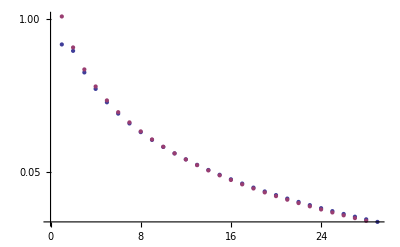

```mathematica
FullSimplify[1/(8 π)√5 (-1+l) l (-1)^l √(9+18/(-1+l)-2/l+2 l) Hypergeometric2F1[2-l,-l,3,-Cot[θ/2]^2] Sin[θ/2]^(-2+2 l)Cos[θ/2]^6,Assumptions->{ϕ∈Reals,θ∈Reals}];
Table[∫_0^π (∫_0^(2π) (%)ⅆϕ)Sin[θ]ⅆθ,{l,2,30}]
ListLogPlot[{%,Table[3/l^(3/2),{l,2,Length[%]}]}]
```

#### More general non-orthogonality

```mathematica
F[l_,m_,s_,lp_,mp_,sp_]:=
(-1)^(l+lp+m+mp+s+sp)2 √((2l+1)/(4π)(2lp+1)/(4π)((l+m)!(l-m)!)/((l+s)!(l-s)!)((lp+mp)!(lp-mp)!)/((lp+sp)!(lp-sp)!))(∫_0^(2π) ⅇ^(ⅈ(m-mp)ϕ)ⅆϕ)(
∑_(ρ=Max[0,m-s])^Min[l-s,l+m] (
∑_(ρp=Max[0,mp-sp])^Min[lp-sp,lp+mp] (
({{l-s}, {ρ}})({{l+s}, {ρ-m+s}})({{lp-sp}, {ρp}})({{lp+sp}, {ρp-mp+sp}})(-1)^(ρ+ρp)(Gamma[1+(2l-2ρ+m-s+2lp-2ρp+mp-sp)/2] Gamma[1+(2ρ-m+s+2ρp-mp+sp)/2])/Gamma[2+l+lp]
)
)
);
```

```mathematica
s=-2; sp=-1;
l=4; lp=3;
m=-2; mp=3;
Table[{F[l,m,s,lp,mp,sp],∫_0^π (∫_0^(2π) (FullSimplify[Y[s,l,m,θ,ϕ],Assumptions->{ϕ∈Reals,θ∈Reals}]Y[sp,lp,mp,θ,ϕ]*)ⅆϕ)Sin[θ]ⅆθ},{m,-l,l},{mp,-lp,lp}]//MatrixForm
```

((0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0)
(-(189 √(15/2) π)/4096
-(189 √(15/2) π)/4096) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0)
(0
0) | (-(189 √(35/2) π)/4096
-(189 √(35/2) π)/4096) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0)
(0
0) | (0
0) | (-(627 √(7/2) π)/4096
-(627 √(7/2) π)/4096) | (0
0) | (0
0) | (0
0) | (0
0)
(0
0) | (0
0) | (0
0) | (-(171 √(105/2) π)/4096
-(171 √(105/2) π)/4096) | (0
0) | (0
0) | (0
0)
(0
0) | (0
0) | (0
0) | (0
0) | (-(627 √(7/2) π)/4096
-(627 √(7/2) π)/4096) | (0
0) | (0
0)
(0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (-(189 √(35/2) π)/4096
-(189 √(35/2) π)/4096) | (0
0)
(0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (-(189 √(15/2) π)/4096
-(189 √(15/2) π)/4096)
(0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0) | (0
0))

#### This tests the agreement with Blanchet et al. (2008), Eq. (2.4). [doi:10.1088/0264-9381/25/16/165003]

```mathematica
YBlanchet[-2,l_,m_,θ_,ϕ_]:=√((2l+1)/(4π))Simplify[∑_(k=Max[0,m-2])^Min[l+m,l-2] (-1)^k/(k!)(√((l+m)!(l-m)!(l+2)!(l-2)!))/((k-m+2)!(l+m-k)!(l-k-2)!)Cos[θ/2]^(2l+m-2k-2)Sin[θ/2]^(2k-m+2)] ⅇ^(ⅈ m ϕ);
Clear[l,m,θ,ϕ]
Table[Simplify[Y[-2,l,m,θ,ϕ]-YBlanchet[-2,l,m,θ,ϕ]],{l,2,9},{m,-l,l}]//MatrixForm
Clear[l,m,θ,ϕ]
```

({0,0,0,0,0}
{0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})